```mathematica
uniqueRoots[f_] := {DeleteDuplicates[Roots[f==0,x]]}

coefficientsToZeros[x_, y_] :=DeleteDuplicates[Sort[Map[Apply[Rational, #]&, Map[Part[#, 1;;2]&, Tuples[{Divisors[x], Divisors[y], {x}}]]]]]

rationalZeros[poly_]:=coefficientsToZeros[First[ CoefficientList[poly, x]], Last[ CoefficientList[poly, x]]]

toPolynomial[coefficients_] := Plus @@ MapIndexed[#1 x^(First[#2]-1) &, Reverse[coefficients]]
```

-4-x+3 x^3+6 x^5

6 x^5+3 x^3-x-4

6 x^5+3 x^3-x-4

{1/6,1/3,1/2,2/3,1,4/3,2,4}

{x==Root[-4-#1+3 #1^3+6 #1^5&,1]||x==ⅈ Im[Root[-4-#1+3 #1^3+6 #1^5&,2]]+Re[Root[-4-#1+3 #1^3+6 #1^5&,2]]||x==ⅈ Im[Root[-4-#1+3 #1^3+6 #1^5&,3]]+Re[Root[-4-#1+3 #1^3+6 #1^5&,3]]||x==ⅈ Im[Root[-4-#1+3 #1^3+6 #1^5&,4]]+Re[Root[-4-#1+3 #1^3+6 #1^5&,4]]||x==ⅈ Im[Root[-4-#1+3 #1^3+6 #1^5&,5]]+Re[Root[-4-#1+3 #1^3+6 #1^5&,5]]}

{6 x^4-18 x^3+57 x^2-171 x+512,-1540}

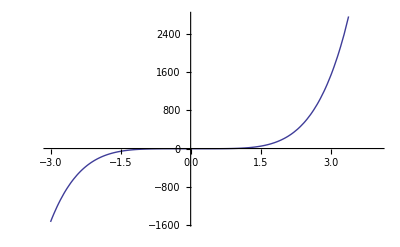

```mathematica
f=6x^5+3x^3-x-4//ExpandAll
(* f=toPolynomial[{2,7,4,-4}] *)
f//TraditionalForm
f//Factor//TraditionalForm
rationalZeros[f]
uniqueRoots[f]//ComplexExpand
PolynomialQuotientRemainder[f, x+3,x]//TraditionalForm
Plot[f, {x, -3, 4}]
```

2 x^4+3 x^3-4 x^2-3 x+2

2 x^4-3 x^3-4 x^2+3 x+2

x==1/2||x==-2||x==-1||x==1

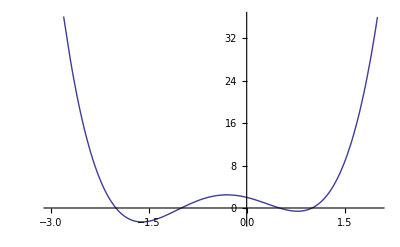

```mathematica
Clear[f, g]
g[x_]:=2x^4+3x^3-4x^2-3x+2
g[x]//TraditionalForm
g[-x]//TraditionalForm
Roots[g[x]==0,x]
Plot[g[x], {x, -3, 2}]
```

```mathematica
PolynomialQuotientRemainder[2+9 x+11 x^2+2 x^3,x+1/2, x]
```

{4+10 x+2 x^2,0}

-1500+(20-2 x) (40-2 x) x

4 x^3-120 x^2+800 x-1500

FindRoot::srect: Value x in search specification {x} is not a number or array of numbers.

FindRoot[v==0,{x}]

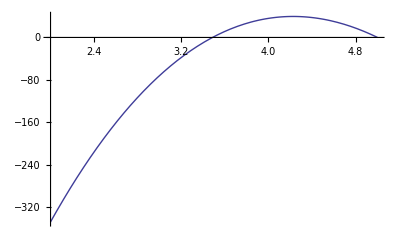

```mathematica
v = x(40-2x)(20-2x)-1500
Expand[v]//TraditionalForm
FindRoot[v==0,{x}]
Plot[v, {x, 2,5}]
```

```mathematica
Roots[4 x^3-120 x^2+800 x-1500==0,x]
```

x==5/2 (5-√13)||x==5/2 (5+√13)||x==5

```mathematica
(20-2 x) (40-2 x) x-1500
```

4 x^3-120 x^2+800 x

```mathematica
1500/4
```

375

```mathematica
f=2x^3-7x^2+4x+4
Roots[f==0,x]
PolynomialQuotientRemainder[f,x-2,x]//TraditionalForm
```

4+4 x-7 x^2+2 x^3

x==-1/2||x==2||x==2

{2 x^2-3 x-2,0}

```mathematica
x^
```

```mathematica
Roots[2x^4+15x^3+31x^2+20x+4==0,x]//TraditionalForm
```

x==1/2 (-5-√17)∨x==1/2 (√17-5)∨x==-1/2∨x==-2

```mathematica
PolynomialQuotient[x^4-5x^3+6x^2+4x-8,x+1,x]//TraditionalForm
```

x^3-6 x^2+12 x-8

```mathematica
ClearAll[f]
```

```mathematica
ClearAll
```

ClearAll

x==-5/2∨x==3/2∨x==-1

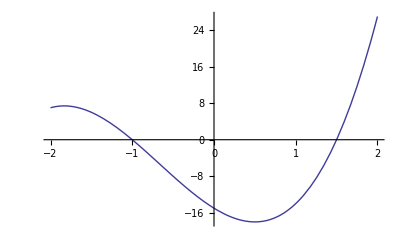

```mathematica
f[x_]:=4x^3+8x^2-11x-15
Roots[f[x]==0,x]//TraditionalForm
Plot[f[x],{x,-2,2}]
```